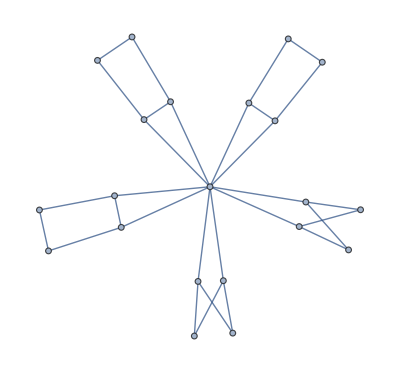
```mathematica
theonlyvalid21=-Graphics-;
adj21=AdjacencyMatrix[theonlyvalid21];
```

```mathematica
Length[all2560]
```

2560

```mathematica
Jacobi[x_,n_,matn_]:=(-22+x) (-2+x)^42 (6+x)^15 (8+x)^2*Det[(x+4)/((x+6)(x-2))IdentityMatrix[n]+matn/((x+6)(x-2))+(9ConstantArray[1,{n,n}])/((x+6)(x-2)(x-22))+((residuemat*(x-14))[[Range[n],Range[n]]]+RA[[Range[n],Range[n]]])/((x+8)(x+6)(x-2)(x-22))];
```

```mathematica
Jacobi[53,21,adj21]
```

16235399957685910857160339368675855206433975230193151623129978226875

```mathematica
coclique22all={};
For[j=1,j≤2560,j++,
mat=ConstantArray[0,{22,22}];
mat[[Range[21],Range[21]]]=adj21;
mat[[22,Range[20]]]=all2560[[j]];
mat[[Range[20],22]]=all2560[[j]];
If[IntegerQ[Jacobi[53,22,mat]],AppendTo[coclique22all,mat]]
]//AbsoluteTiming
coclique22all//Length
```

{3.10365,Null}

454

```mathematica
coclique22graphs=Array[coclique22g,Length[coclique22all]];
For[i=1,i≤Length[coclique22all],i++,
coclique22graphs[[i]]=AdjacencyGraph[coclique22all[[i]]]
]
coclique22=DeleteDuplicatesBy[coclique22graphs,CanonicalGraph];
Length[coclique22]
```

7

```mathematica
all454={};
For[j=1,j≤2560,j++,
mat=ConstantArray[0,{22,22}];
mat[[Range[21],Range[21]]]=adj21;
mat[[22,Range[20]]]=all2560[[j]];
mat[[Range[20],22]]=all2560[[j]];
If[IntegerQ[Jacobi[53,22,mat]],AppendTo[all454,all2560[[j]]]]
]//AbsoluteTiming
all454//Length
```

{3.185,Null}

454

```mathematica
all454={{0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,0,1,0,1,0},{0,0,1,1,0,1,1,0,0,1,1,0,1,0,1,0,1,0,1,0},{0,0,1,1,0,1,1,0,1,0,0,1,1,0,1,0,1,0,1,0},{0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,1,1,0,1,0},{0,0,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,1,0,1},{0,0,1,1,1,0,0,1,0,1,1,0,1,0,1,0,1,0,1,0},{0,0,1,1,1,0,0,1,1,0,0,1,1,0,1,0,1,0,1,0},{0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,1,1,0,1,0},{0,0,1,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1,0,1},{0,0,1,1,1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0},{0,0,1,1,1,1,0,0,0,1,1,0,0,1,0,1,1,0,1,0},{0,0,1,1,1,1,0,0,0,1,1,0,1,0,1,0,0,1,0,1},{0,0,1,1,1,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0},{0,0,1,1,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,1},{0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0,1,1,0},{0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0,0},{0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,0,1,1},{0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0},{0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0,0},{0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0,0},{0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,0,0,1,1},{0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,0,1,1,0},{0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0,1,1,0,0},{0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,1},{0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1,0},{0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,1,0,0,1},{0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,1,1,0,0},{0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,0,1,1},{0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0,1,0,0,1},{0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,0},{0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0},{0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0},{0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1},{0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,0,1,1,0},{0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,1,0,0,1},{0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0,1,1,0,0},{0,1,0,1,0,1,1,0,0,1,0,1,0,0,1,1,0,0,1,1},{0,1,0,1,0,1,1,0,0,1,0,1,0,0,1,1,0,1,1,0},{0,1,0,1,0,1,1,0,0,1,0,1,0,0,1,1,1,0,0,1},{0,1,0,1,0,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0},{0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,0,1,1},{0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,0},{0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,0,1,0,0,1},{0,1,0,1,0,1,1,0,0,1,0,1,0,1,1,0,1,1,0,0},{0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,0,1,1},{0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0},{0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1},{0,1,0,1,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0},{0,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1},{0,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,0,1,1,0},{0,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,1,0,0,1},{0,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,1,0,0,1,1},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,1,0,1,1,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,1,1,0,0,1},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,1,1,1,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,1},{0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1,1,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,1,0,0,1},{0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,1,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,0,1,1},{0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0},{0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,1},{0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,0,1,1,0},{0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,1,0,0,1},{0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,0,1,1,0,0},{0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,1,0,0,1,1},{0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,1,0,1,1,0},{0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,1,1,0,0,1},{0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0},{0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,0,1,1},{0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0},{0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1},{0,1,0,1,1,0,0,1,0,1,0,1,0,1,1,0,1,1,0,0},{0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,0,0,1,1},{0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,0,1,1,0},{0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,1},{0,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,1,0,0},{0,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,0,0,1,1},{0,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,0,1,1,0},{0,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,1,0,0,1},{0,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,1,1,0,0},{0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,0,0,1,1},{0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,0},{0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1},{0,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,1,1,0,0},{0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,0,1,1},{0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0},{0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,1,0,0,1},{0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,1,1,0,0},{0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,1,0,0,1,1},{0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,1,0,1,1,0},{0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,1,1,0,0,1},{0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,1,1,1,0,0},{0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,0,0,1,1},{0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,0,1,1,0},{0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,0,0,1},{0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,0},{0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,0,0,1,1},{0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,0,1,1,0},{0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,1,0,0,1},{0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1,1,1,0,0},{0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,0,1,1},{0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0},{0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1},{0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,1,1,0,0},{0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,1},{0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1,0,1,1,0},{0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1},{0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1,1,1,0,0},{0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0,0,0,1,1},{0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0},{0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1},{0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0,1,1,0,0},{0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1},{0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,0,1,1,0},{0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,0,0,1},{0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,0},{0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,0,1,1},{0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,1,1,0},{0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1},{0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,0},{0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1,0,0,1,1},{0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1,0,1,1,0},{0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1},{0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,0,0},{0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,0,0,1,1},{0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,0,1,1,0},{0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,1,0,0,1},{0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,1,1,0,0},{0,1,1,0,0,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0},{0,1,1,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,0},{0,1,1,0,0,0,1,1,1,1,0,0,0,1,0,1,1,0,1,0},{0,1,1,0,0,0,1,1,1,1,0,0,1,0,1,0,0,1,0,1},{0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1},{0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0},{0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1},{0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,1,1,1,0,0},{0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1},{0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0},{0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1},{0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1},{0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0},{0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1},{0,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0},{0,1,1,0,0,1,0,1,0,1,0,1,1,1,0,0,0,0,1,1},{0,1,1,0,0,1,0,1,0,1,0,1,1,1,0,0,0,1,1,0},{0,1,1,0,0,1,0,1,0,1,0,1,1,1,0,0,1,0,0,1},{0,1,1,0,0,1,0,1,0,1,0,1,1,1,0,0,1,1,0,0},{0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0,0,1,1},{0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0,1,1,0},{0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,1,0,0,1},{0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,1,1,0,0},{0,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1},{0,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0},{0,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1},{0,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1},{0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0},{0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1},{0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0},{0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,1},{0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,0,0,1,1,0},{0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,0,1,0,0,1},{0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,0,1,1,0,0},{0,1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,0,1,0},{0,1,1,0,0,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0},{0,1,1,0,0,1,1,0,0,1,1,0,1,0,1,0,0,1,0,1},{0,1,1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0},{0,1,1,0,0,1,1,0,1,0,0,1,1,0,1,0,0,1,0,1},{0,1,1,0,0,1,1,0,1,1,0,0,0,1,0,1,0,1,0,1},{0,1,1,0,1,0,0,1,0,0,1,1,1,0,1,0,1,0,1,0},{0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,0},{0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,1},{0,1,1,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,1,0},{0,1,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,0,1},{0,1,1,0,1,0,0,1,1,1,0,0,0,1,0,1,0,1,0,1},{0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,0,0,1,1},{0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,0,1,1,0},{0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,0,0,1},{0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0},{0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1},{0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0},{0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1},{0,1,1,0,1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0},{0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1},{0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0},{0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1},{0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0},{0,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,0,0,1,1},{0,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,0,1,1,0},{0,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,1,0,0,1},{0,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,1,1,0,0},{0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,1,0,0,1,1},{0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0},{0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,0,0,1},{0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,1,1,1,0,0},{0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1},{0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0},{0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1},{0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0},{0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1},{0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0},{0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1},{0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0},{0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0},{0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1},{0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0},{0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,0,1,0},{0,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,1,0,1},{0,1,1,0,1,1,0,0,0,1,1,0,0,1,0,1,0,1,0,1},{0,1,1,0,1,1,0,0,1,0,0,1,0,1,0,1,0,1,0,1},{1,0,0,1,0,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0},{1,0,0,1,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,0},{1,0,0,1,0,0,1,1,1,1,0,0,0,1,0,1,1,0,1,0},{1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1},{1,0,0,1,0,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0},{1,0,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1},{1,0,0,1,0,1,0,1,0,1,0,1,0,0,1,1,1,1,0,0},{1,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1},{1,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0},{1,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,0},{1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1},{1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1},{1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,1,0,0},{1,0,0,1,0,1,0,1,0,1,0,1,1,1,0,0,0,0,1,1},{1,0,0,1,0,1,0,1,0,1,0,1,1,1,0,0,0,1,1,0},{1,0,0,1,0,1,0,1,0,1,0,1,1,1,0,0,1,0,0,1},{1,0,0,1,0,1,0,1,0,1,0,1,1,1,0,0,1,1,0,0},{1,0,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0,0,1,1},{1,0,0,1,0,1,0,1,1,0,1,0,0,0,1,1,0,1,1,0},{1,0,0,1,0,1,0,1,1,0,1,0,0,0,1,1,1,0,0,1},{1,0,0,1,0,1,0,1,1,0,1,0,0,0,1,1,1,1,0,0},{1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,0,1,1},{1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0},{1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1},{1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0},{1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1},{1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0},{1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,1},{1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0},{1,0,0,1,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,1},{1,0,0,1,0,1,0,1,1,0,1,0,1,1,0,0,0,1,1,0},{1,0,0,1,0,1,0,1,1,0,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,0,1,0,1,1,0,1,0,1,1,0,0,1,1,0,0},{1,0,0,1,0,1,1,0,0,0,1,1,1,0,1,0,1,0,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0},{1,0,0,1,0,1,1,0,1,0,0,1,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,0,1,0,1},{1,0,0,1,1,0,0,1,0,0,1,1,1,0,1,0,1,0,1,0},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,0},{1,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,1},{1,0,0,1,1,0,0,1,1,0,0,1,0,1,0,1,1,0,1,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,1,0,1},{1,0,0,1,1,0,0,1,1,1,0,0,0,1,0,1,0,1,0,1},{1,0,0,1,1,0,1,0,0,1,0,1,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,1,0,0,1,0,1,0,0,1,1,0,1,1,0},{1,0,0,1,1,0,1,0,0,1,0,1,0,0,1,1,1,0,0,1},{1,0,0,1,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0},{1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1},{1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1},{1,0,0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0},{1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1},{1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0},{1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0},{1,0,0,1,1,0,1,0,0,1,0,1,1,1,0,0,0,0,1,1},{1,0,0,1,1,0,1,0,0,1,0,1,1,1,0,0,0,1,1,0},{1,0,0,1,1,0,1,0,0,1,0,1,1,1,0,0,1,0,0,1},{1,0,0,1,1,0,1,0,0,1,0,1,1,1,0,0,1,1,0,0},{1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0},{1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,1,0,0,1},{1,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,1,1,0,0},{1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1},{1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0},{1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1},{1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0},{1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1},{1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0},{1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1},{1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0},{1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0},{1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0},{1,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,1,0,1,0},{1,0,0,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,0,1},{1,0,0,1,1,1,0,0,0,1,1,0,0,1,0,1,0,1,0,1},{1,0,0,1,1,1,0,0,1,0,0,1,0,1,0,1,0,1,0,1},{1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1,0,0,1,1},{1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1,0,1,1,0},{1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1,1,0,0,1},{1,0,1,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,0,1,1},{1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0},{1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0,1,0,0,1},{1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0,0},{1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,0,1,1},{1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1},{1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,1,0,0},{1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0,0,1,1,0},{1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,0,0,1,0,1,0,1,1,0,1,1,0,0,1,1,0,0},{1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1,0},{1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,1,0,0,1},{1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,0,0,1},{1,0,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,0},{1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0},{1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0},{1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0,0,1,1,0},{1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,0,0,1},{1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,1,0,0},{1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,0,0,1,1},{1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,0,1,1,0},{1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,1,0,0,1},{1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,0,0,1,1},{1,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,0},{1,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,1,0,0,1},{1,0,1,0,0,1,1,0,0,1,0,1,0,1,1,0,1,1,0,0},{1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,0,0,1,1},{1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0},{1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,1},{1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0},{1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,1,0},{1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,0,0,1},{1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,1,0,0},{1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,1,0,0,1,1},{1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,1,0,1,1,0},{1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,1,1,0,0,1},{1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,1,1,1,0,0},{1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,0,0,0,1,1},{1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,0,0,1,1,0},{1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,0,1,0,0,1},{1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,0,1,1,0,0},{1,0,1,0,0,1,1,0,1,0,1,0,1,0,0,1,0,0,1,1},{1,0,1,0,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0},{1,0,1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,1},{1,0,1,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,0},{1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,0,1,1,0},{1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,1,0,0,1},{1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,0,1,0,1,0,1,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,1,0},{1,0,1,0,1,0,0,1,0,1,0,1,0,0,1,1,1,0,0,1},{1,0,1,0,1,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0},{1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,0,0,1,1},{1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0},{1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1},{1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,1,0,0},{1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,1,0,0,1,1},{1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,1,0,1,1,0},{1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,1},{1,0,1,0,1,0,0,1,0,1,0,1,1,0,0,1,1,1,0,0},{1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,0,0,1,1},{1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,0,1,1,0},{1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,1,0,0,1},{1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,0,1,1,0,1,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,0},{1,0,1,0,1,0,0,1,1,0,1,0,0,0,1,1,1,0,0,1},{1,0,1,0,1,0,0,1,1,0,1,0,0,0,1,1,1,1,0,0},{1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,0,1,1},{1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0},{1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,1,0,0,1},{1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,1,1,0,0},{1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,1,0,0,1,1},{1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,1,0,1,1,0},{1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,0,0,1},{1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,1,1,1,0,0},{1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,0,0,0,1,1},{1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,0,0,1,1,0},{1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,0,1,0,0,1},{1,0,1,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,1,0,0,1},{1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,1,1,0,0},{1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1},{1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,1,1,0,0},{1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1},{1,0,1,0,1,0,1,0,0,1,1,0,1,0,0,1,1,1,0,0},{1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,0,0,1,1},{1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,0,1,1,0},{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0,0,1,1,0},{1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,0,1,1,0},{1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,1,1,0,0},{1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,0,1,1,0},{1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,1,0,0},{1,1,0,0,0,0,1,1,0,0,1,1,1,0,1,0,1,0,1,0},{1,1,0,0,0,0,1,1,0,1,1,0,0,1,0,1,1,0,1,0},{1,1,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,1,1,0,0,1,0,1,0,1,1,0,1,0},{1,1,0,0,0,0,1,1,1,0,0,1,1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,1,1,1,0,0,0,1,0,1,0,1,0,1},{1,1,0,0,0,1,1,0,0,0,1,1,0,1,0,1,1,0,1,0},{1,1,0,0,0,1,1,0,0,0,1,1,1,0,1,0,0,1,0,1},{1,1,0,0,0,1,1,0,0,1,1,0,0,1,0,1,0,1,0,1},{1,1,0,0,0,1,1,0,1,0,0,1,0,1,0,1,0,1,0,1},{1,1,0,0,1,0,0,1,0,0,1,1,0,1,0,1,1,0,1,0},{1,1,0,0,1,0,0,1,0,0,1,1,1,0,1,0,0,1,0,1},{1,1,0,0,1,0,0,1,0,1,1,0,0,1,0,1,0,1,0,1},{1,1,0,0,1,0,0,1,1,0,0,1,0,1,0,1,0,1,0,1},{1,1,0,0,1,1,0,0,0,0,1,1,0,1,0,1,0,1,0,1}};
```

```mathematica
Length[all454]
```

454

```mathematica
coclique22all//Length
```

454

```mathematica
coclique23allfrom22all={};
For[i=1,i≤454,i++,
n=23;
If[Mod[i,10]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=coclique22all[[i]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique23allfrom22all,mat]]
]
]//AbsoluteTiming
coclique23allfrom22all//Length
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

370

380

390

400

410

420

430

440

450

{300.39,Null}

37080

```mathematica
coclique23graphsfrom22all=Array[coclique23g22all,Length[coclique23allfrom22all]];
For[i=1,i≤Length[coclique23allfrom22all],i++,
coclique23graphsfrom22all[[i]]=AdjacencyGraph[coclique23allfrom22all[[i]]]
]
coclique23from22all=DeleteDuplicatesBy[coclique23graphsfrom22all,CanonicalGraph];
Length[coclique23from22all]
```

30

```mathematica
coclique23all={};
For[i=1,i≤7,i++,
n=23;
Print[i];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique22[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique23all,mat]]
]
]//AbsoluteTiming
coclique23all//Length
```

1

2

3

4

5

6

7

{4.25689,Null}

1556

```mathematica
coclique23graphs=Array[coclique23g,Length[coclique23all]];
For[i=1,i≤Length[coclique23all],i++,
coclique23graphs[[i]]=AdjacencyGraph[coclique23all[[i]]]
]
coclique23=DeleteDuplicatesBy[coclique23graphs,CanonicalGraph];
Length[coclique23]
```

30

```mathematica
coclique24all454={};
For[i=1,i≤30,i++,
n=24;
If[Mod[i,3]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique23[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique24all454,mat]]
]
]//AbsoluteTiming
coclique24all454//Length
```

3

6

9

12

15

18

21

24

27

30

{20.0645,Null}

2924

```mathematica
coclique24all2560={};
For[i=1,i≤30,i++,
n=24;
If[Mod[i,3]==0,Print[i]];
For[j=1,j≤2560,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique23[[i]]];
mat[[n,Range[20]]]=all2560[[j]];
mat[[Range[20],n]]=all2560[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique24all2560,mat]]
]
]//AbsoluteTiming
coclique24all2560//Length
```

3

6

9

12

15

18

21

24

27

30

{120.922,Null}

3004

```mathematica
Intersection[coclique24all454,coclique24all2560]//Length
```

2924

```mathematica
Complement[coclique24all2560,coclique24all454]//Length
```

80

```mathematica
coclique23[[9]]//AdjacencyMatrix//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
Complement[coclique24all2560,coclique24all454][[1]]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
A=({{0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1}, {1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 1}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1}, {0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 1, 0, 0, 1, 1, 0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 1, 1, 1, 0, 0, 0, 1, 0, 1, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 0, 1, 0, 0, 1, 1, 1, 0, 1, 0, 0, 0, 0, 0}});
```

```mathematica
Range[24]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
ran={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,24};
```

```mathematica
Jacobi[53,21,A[[ran,ran]]]
```

16235399957685910857160339368675855206433975230193151623129978226875

```mathematica
coclique24graphs454=Array[coclique24g,Length[coclique24all454]];
For[i=1,i≤Length[coclique24all454],i++,
coclique24graphs454[[i]]=AdjacencyGraph[coclique24all454[[i]]]
]
coclique24n454=DeleteDuplicatesBy[coclique24graphs454,CanonicalGraph];
Length[coclique24n454]
```

171

```mathematica
coclique24graphs2560=Array[coclique24g,Length[coclique24all2560]];
For[i=1,i≤Length[coclique24all2560],i++,
coclique24graphs2560[[i]]=AdjacencyGraph[coclique24all2560[[i]]]
]
coclique24n2560=DeleteDuplicatesBy[coclique24graphs2560,CanonicalGraph];
Length[coclique24n2560]
```

187

```mathematica
coclique24refined={};
For[i=1,i≤Length[coclique24],i++,
If[Mod[i,4]==0,Print[i]];
If[PolynomialQ[Jacobi[x,24,AdjacencyMatrix[coclique24[[i]]]]//Factor,x],AppendTo[coclique24refined,coclique24[[i]]]]
]//AbsoluteTiming
coclique24refined//Length
```

4

8

12

16

20

24

28

32

36

40

44

48

52

56

60

64

68

72

76

80

84

88

92

96

100

104

108

112

116

120

124

128

132

136

140

144

148

152

156

160

164

168

172

176

180

184

{152.077,Null}

171

```mathematica
coclique25all={};
For[i=1,i≤171,i++,
n=25;
If[Mod[i,5]==0,Print[i]];
For[j=1,j≤2560,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique24refined[[i]]];
mat[[n,Range[20]]]=all2560[[j]];
mat[[Range[20],n]]=all2560[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique25all,mat]]
]
]//AbsoluteTiming
coclique25all//Length
```

5

10

15

20

25

30

35

40

45

50

55

60

65

70

75

80

85

90

95

100

105

110

115

120

125

130

135

140

145

150

155

160

165

170

{890.125,Null}

6608

```mathematica
coclique25graphs=Array[coclique25g,Length[coclique25all]];
For[i=1,i≤Length[coclique25all],i++,
coclique25graphs[[i]]=AdjacencyGraph[coclique25all[[i]]]
]
coclique25=DeleteDuplicatesBy[coclique25graphs,CanonicalGraph];
Length[coclique25]
```

467

```mathematica
coclique25refined={};
For[i=1,i≤Length[coclique25],i++,
If[Mod[i,10]==0,Print[i]];
If[PolynomialQ[Jacobi[x,25,AdjacencyMatrix[coclique25[[i]]]]//Factor,x],AppendTo[coclique25refined,coclique25[[i]]]]
]//AbsoluteTiming
coclique25refined//Length
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

370

380

390

400

410

420

430

440

450

460

{491.361,Null}

467

```mathematica
coclique26all={};
For[i=1,i≤467,i++,
n=26;
If[Mod[i,15]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique25refined[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique26all,mat]]
]
]//AbsoluteTiming
coclique26all//Length
```

15

30

45

60

75

90

105

120

135

150

165

180

195

210

225

240

255

270

285

300

315

330

345

360

375

390

405

420

435

450

465

{461.459,Null}

6706

```mathematica
coclique26graphs=Array[coclique26g,Length[coclique26all]];
For[i=1,i≤Length[coclique26all],i++,
coclique26graphs[[i]]=AdjacencyGraph[coclique26all[[i]]]
]
coclique26=DeleteDuplicatesBy[coclique26graphs,CanonicalGraph];
Length[coclique26]
```

1007

```mathematica
coclique26refined={};
For[i=1,i≤Length[coclique26],i++,
If[Mod[i,20]==0,Print[i]];
If[PolynomialQ[Jacobi[x,26,AdjacencyMatrix[coclique26[[i]]]]//Factor,x],AppendTo[coclique26refined,coclique26[[i]]]]
]//AbsoluteTiming
coclique26refined//Length
```

20

40

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

880

900

920

940

960

980

1000

{1312.64,Null}

965

```mathematica
coclique27all={};
For[i=1,i≤965,i++,
n=27;
If[Mod[i,20]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique26refined[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique27all,mat]]
]
]//AbsoluteTiming
coclique27all//Length
```

20

40

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

880

900

920

940

960

{985.47,Null}

7140

```mathematica
coclique27graphs=Array[coclique27g,Length[coclique27all]];
For[i=1,i≤Length[coclique27all],i++,
coclique27graphs[[i]]=AdjacencyGraph[coclique27all[[i]]]
]
coclique27=DeleteDuplicatesBy[coclique27graphs,CanonicalGraph];
Length[coclique27]
```

1113

```mathematica
coclique27refined={};
For[i=1,i≤Length[coclique27],i++,
If[Mod[i,20]==0,Print[i]];
If[PolynomialQ[Jacobi[x,27,AdjacencyMatrix[coclique27[[i]]]]//Factor,x],AppendTo[coclique27refined,coclique27[[i]]]]
]//AbsoluteTiming
coclique27refined//Length
```

20

40

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

880

900

920

940

960

980

1000

1020

1040

1060

1080

1100

{1721.29,Null}

879

```mathematica
coclique28all={};
For[i=1,i≤879,i++,
n=28;
If[Mod[i,20]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique27refined[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique28all,mat]]
]
]//AbsoluteTiming
coclique28all//Length
```

20

40

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

{991.886,Null}

2030

```mathematica
coclique28graphs=Array[coclique28g,Length[coclique28all]];
For[i=1,i≤Length[coclique28all],i++,
coclique28graphs[[i]]=AdjacencyGraph[coclique28all[[i]]]
]
coclique28=DeleteDuplicatesBy[coclique28graphs,CanonicalGraph];
Length[coclique28]
```

665

```mathematica
coclique28refined={};
For[i=1,i≤Length[coclique28],i++,
If[Mod[i,15]==0,Print[i]];
If[PolynomialQ[Jacobi[x,28,AdjacencyMatrix[coclique28[[i]]]]//Factor,x],AppendTo[coclique28refined,coclique28[[i]]]]
]//AbsoluteTiming
coclique28refined//Length
```

15

30

45

60

75

90

105

120

135

150

165

180

195

210

225

240

255

270

285

300

315

330

345

360

375

390

405

420

435

450

465

480

495

510

525

540

555

570

585

600

615

630

645

660

{1172.59,Null}

417

```mathematica
deg10n29={};
For[i=1,i≤417,i++,
val=AdjacencyMatrix[coclique28refined[[i]]].ConstantArray[1,28];
For[j=1,j≤20,j++,
If[val[[j]]==10,AppendTo[deg10n29,i];Print[i," ",val];Break[]]
]
]
deg10n29//Length
```

43 {4,8,4,8,6,6,6,6,6,6,6,6,6,4,10,4,8,4,8,4,10,10,10,10,10,10,10,10}

46 {6,6,6,6,6,6,6,6,6,6,6,6,6,2,10,6,8,4,8,4,10,10,10,10,10,10,10,10}

47 {4,8,4,8,6,6,6,6,6,6,6,6,6,4,10,4,8,4,8,4,10,10,10,10,10,10,10,10}

49 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,6,4,10,4,10,10,10,10,10,10,10,10}

50 {4,8,4,8,6,6,6,6,6,6,6,6,6,4,10,4,8,4,8,4,10,10,10,10,10,10,10,10}

53 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,8,2,8,6,10,10,10,10,10,10,10,10}

61 {6,6,6,6,6,6,6,6,6,6,6,6,6,2,10,6,8,4,8,4,10,10,10,10,10,10,10,10}

62 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,6,4,10,4,10,10,10,10,10,10,10,10}

63 {6,6,6,6,6,6,6,6,6,6,6,6,8,2,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

66 {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,10,2,10,2,10,10,10,10,10,10,10,10}

125 {4,8,4,8,6,6,6,6,4,10,4,6,6,6,6,6,8,4,8,4,10,10,10,10,10,10,10,10}

139 {4,8,4,8,6,6,6,6,6,8,6,4,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

141 {4,8,4,8,6,6,6,6,6,8,6,4,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

152 {6,6,6,6,6,6,6,6,4,10,4,6,4,6,8,6,8,4,8,4,10,10,10,10,10,10,10,10}

153 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

154 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

155 {6,6,6,6,6,6,6,6,4,10,4,6,4,6,8,6,8,4,8,4,10,10,10,10,10,10,10,10}

156 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,8,2,8,6,10,10,10,10,10,10,10,10}

158 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

159 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,8,2,8,6,10,10,10,10,10,10,10,10}

160 {6,6,6,6,6,6,6,6,6,8,6,4,6,6,6,6,6,2,10,6,10,10,10,10,10,10,10,10}

162 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

165 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

167 {6,6,6,6,6,6,6,6,6,8,6,4,6,6,6,6,6,2,10,6,10,10,10,10,10,10,10,10}

171 {6,6,6,6,6,6,6,6,8,6,8,2,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

177 {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,10,2,10,2,10,10,10,10,10,10,10,10}

178 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

183 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

184 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

185 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

193 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

194 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

195 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

199 {4,8,4,8,6,6,6,6,6,10,2,6,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

201 {4,8,4,8,6,6,6,6,6,10,2,6,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

213 {6,6,6,6,6,6,6,6,6,10,2,6,4,6,8,6,6,6,6,6,10,10,10,10,10,10,10,10}

215 {6,6,6,6,6,6,6,6,6,10,2,6,4,6,8,6,6,6,6,6,10,10,10,10,10,10,10,10}

221 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

240 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

241 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

242 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

244 {4,8,4,8,6,6,6,6,6,6,6,6,6,4,10,4,8,4,8,4,10,10,10,10,10,10,10,10}

253 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,6,4,10,4,10,10,10,10,10,10,10,10}

256 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,6,4,10,4,10,10,10,10,10,10,10,10}

259 {4,8,4,8,6,6,6,6,6,6,6,6,6,4,10,4,8,4,8,4,10,10,10,10,10,10,10,10}

270 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,8,2,8,6,10,10,10,10,10,10,10,10}

273 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,8,2,8,6,10,10,10,10,10,10,10,10}

291 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

292 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

293 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

299 {6,6,6,6,6,6,6,6,6,6,6,6,6,2,10,6,8,4,8,4,10,10,10,10,10,10,10,10}

300 {6,6,6,6,6,6,6,6,6,6,6,6,6,4,10,4,6,4,10,4,10,10,10,10,10,10,10,10}

301 {6,6,6,6,6,6,6,6,6,6,6,6,8,2,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

364 {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,10,2,10,2,10,10,10,10,10,10,10,10}

365 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

373 {6,6,6,6,4,8,4,8,6,8,6,4,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

377 {6,6,6,6,6,6,6,6,4,10,4,6,4,6,8,6,8,4,8,4,10,10,10,10,10,10,10,10}

378 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,6,4,10,4,10,10,10,10,10,10,10,10}

379 {6,6,6,6,6,6,6,6,4,10,4,6,6,6,6,6,8,2,8,6,10,10,10,10,10,10,10,10}

382 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

383 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

384 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

388 {6,6,6,6,6,6,6,6,6,8,6,4,6,6,6,6,6,2,10,6,10,10,10,10,10,10,10,10}

389 {6,6,6,6,6,6,6,6,6,8,6,4,4,6,8,6,6,4,10,4,10,10,10,10,10,10,10,10}

395 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

405 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

406 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

416 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

417 {6,6,6,6,6,6,6,6,6,10,6,2,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10}

69

```mathematica
deg10n29
```

{43,46,47,49,50,53,61,62,63,66,125,139,141,152,153,154,155,156,158,159,160,162,165,167,171,177,178,183,184,185,193,194,195,199,201,213,215,221,240,241,242,244,253,256,259,270,273,291,292,293,299,300,301,364,365,373,377,378,379,382,383,384,388,389,395,405,406,416,417}

```mathematica
coclique28refined[[405]]//AdjacencyMatrix//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

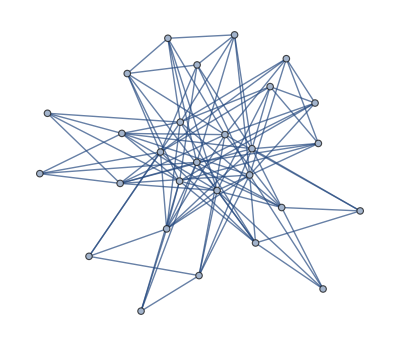
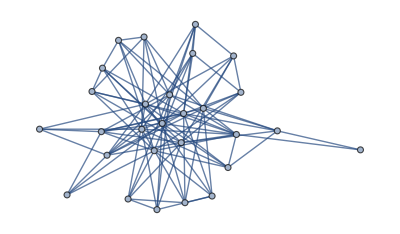
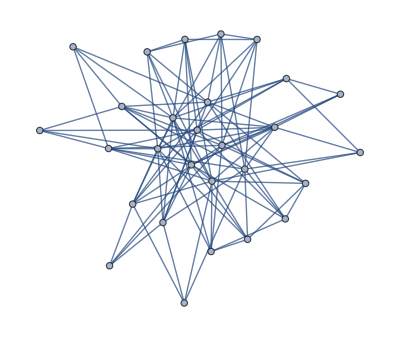
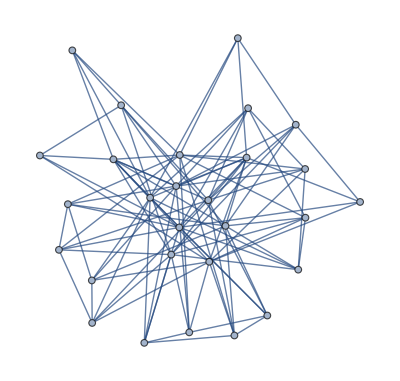
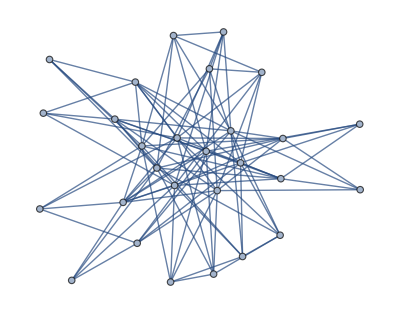
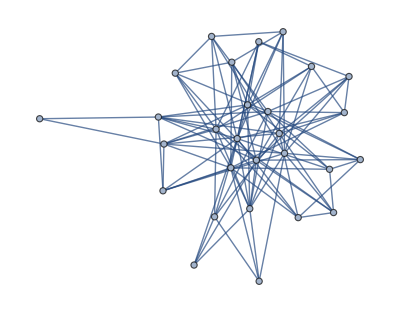
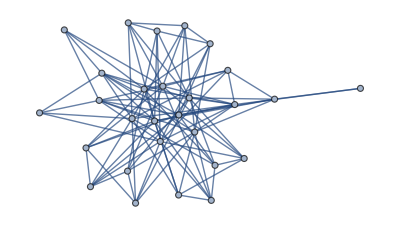
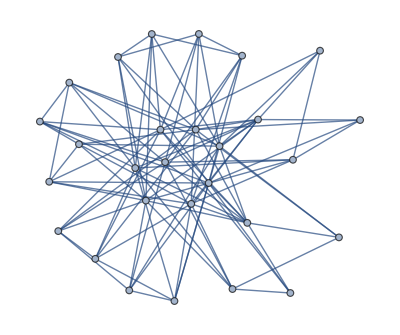
```mathematica
coclique28deg10={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
AdjacencyMatrix[-Graphics-]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FindGraphIsomorphism[-Graphics-,-Graphics-,All]
```

{<|1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10,11→11,12→12,13→13,14→14,15→15,16→16,17→17,18→18,19→19,20→20,21→21,22→22,23→23,24→24,25→25,26→26,27→27,28→28|>,<|1→5,2→6,3→7,4→8,5→1,6→2,7→3,8→4,9→9,10→10,11→11,12→12,13→17,14→18,15→19,16→20,17→13,18→14,19→15,20→16,21→21,22→25,23→23,24→27,25→22,26→26,27→24,28→28|>,<|1→16,2→15,3→14,4→13,5→20,6→19,7→18,8→17,9→11,10→10,11→9,12→12,13→8,14→7,15→6,16→5,17→4,18→3,19→2,20→1,21→23,22→24,23→21,24→25,25→27,26→28,27→22,28→26|>,<|1→20,2→19,3→18,4→17,5→16,6→15,7→14,8→13,9→11,10→10,11→9,12→12,13→4,14→3,15→2,16→1,17→8,18→7,19→6,20→5,21→23,22→27,23→21,24→22,25→24,26→28,27→25,28→26|>}

```mathematica
GraphAutomorphismGroup[-Graphics-]
```

PermutationGroup[{Cycles[{{1,5},{2,6},{3,7},{4,8},{13,17},{14,18},{15,19},{16,20},{22,25},{24,27}}],Cycles[{{1,16,5,20},{2,15,6,19},{3,14,7,18},{4,13,8,17},{9,11},{21,23},{22,24,25,27},{26,28}}]}]

```mathematica
GroupOrder[%6]
```

4

```mathematica
coclique29all={};
For[i=1,i≤417,i++,
n=29;
If[Mod[i,15]==0,Print[i]];
For[j=1,j≤454,j++,
mat=ConstantArray[0,{n,n}];
mat[[Range[n-1],Range[n-1]]]=AdjacencyMatrix[coclique28refined[[i]]];
mat[[n,Range[20]]]=all454[[j]];
mat[[Range[20],n]]=all454[[j]];
If[IntegerQ[Jacobi[53,n,mat]],AppendTo[coclique29all,mat]]
]
]//AbsoluteTiming
coclique29all//Length
```

15

30

45

60

75

90

105

120

135

150

165

180

195

210

225

240

255

270

285

300

315

330

345

360

375

390

405

{516.183,Null}

128

```mathematica
coclique29graphs=Array[coclique29g,Length[coclique29all]];
For[i=1,i≤Length[coclique29all],i++,
coclique29graphs[[i]]=AdjacencyGraph[coclique29all[[i]]]
]
coclique29=DeleteDuplicatesBy[coclique29graphs,CanonicalGraph];
Length[coclique29]
```

56

```mathematica
AdjacencyMatrix[coclique29[[56]]].ConstantArray[1,29]
```

{4,7,5,10,7,8,5,6,8,7,6,5,8,4,7,7,7,5,8,6,10,10,10,10,10,10,10,10,10}

```mathematica
Jacobi[53,29,AdjacencyMatrix[coclique29[[56]]]]
Jacobi[x,29,AdjacencyMatrix[coclique29[[56]]]]//Factor
```

270260461526483871266743056343762377305573244790078125

((-2+x)^14 (2+x)^3 (4+x) (2+4 x+x^2)^2 (36096+139200 x+72352 x^2-207392 x^3-336000 x^4-218340 x^5-74364 x^6-12986 x^7-686 x^8+128 x^9+22 x^10+x^11))/(6+x)^2

```mathematica
coclique29refined={};
For[i=1,i≤Length[coclique29],i++,
If[Mod[i,4]==0,Print[i]];
If[PolynomialQ[Jacobi[x,29,AdjacencyMatrix[coclique29[[i]]]]//Factor,x],AppendTo[coclique29refined,coclique29[[i]]]]
]//AbsoluteTiming
coclique29refined//Length
```

4

8

12

16

20

24

28

32

36

40

44

48

52

56

{113.802,Null}

0

```mathematica
Length[coclique29all]
```

128

```mathematica
coclique29nomodiso={};
For[i=1,i≤Length[coclique29all],i++,
If[Mod[i,4]==0,Print[i]];
If[PolynomialQ[Jacobi[x,29,coclique29all[[i]]]//Factor,x],AppendTo[coclique29nomodiso,coclique29all[[i]]]]
]//AbsoluteTiming
coclique29nomodiso//Length
```

4

8

12

16

20

24

28

32

36

40

44

48

52

56

60

64

68

72

76

80

84

88

92

96

100

104

108

112

116

120

124

128

{260.534,Null}

0